```mathematica
ClearAll
H = 2p(1-p)
B= 1-p^2

NH = Simplify[1-H]
NB= Simplify[1-B]
```

ClearAll

2 (1-p) p

1-p^2

1-2 p+2 p^2

p^2

```mathematica
BgH = 1

Clear[BgNH]
s=Solve[B == BgH*H + BgNH*NH, BgNH]
BgNH=Simplify[s[[1,1,2]]]
```

1

{{BgNH→(1-2 p+p^2)/(1-2 p+2 p^2)}}

(-1+p)^2/(1-2 p+2 p^2)

```mathematica
NBgNH = p^2/NH
Simplify[BgNH+NBgNH]
```

p^2/(1-2 p+2 p^2)

1

```mathematica
Simplify[2p(1-p)+(p-1)^2+p^2]
```

1

```mathematica
XgBH = xgBH = 1/2
XBH = H*BgH*XgBH
xBH = H*BgH*xgBH
```

1/2

(1-p) p

(1-p) p

```mathematica
XgBNH = 1
XBNH = XgBNH*BgNH*NH

xgNBNH = 1
xNBNH = xgNBNH*NBgNH*NH
```

1

(-1+p)^2

1

p^2

```mathematica
Simplify[XBH+xBH+XBNH+xNBNH]
```

1

```mathematica
X=Simplify[XBH+XBNH]
x=Simplify[xBH+xNBNH]
```

1-p

p

```mathematica
cXX=X*X
cxX=x*X
cXx=X*x
cxx=x*x
Simplify[cXX+cXx+cxX+cxx]
```

(1-p)^2

(1-p) p

(1-p) p

p^2

2 (1-p) p

(1-p)^2+2 (1-p) p

1

```mathematica
cH=Simplify[cxX+cXx]
cB=Simplify[cH+cXX]
```

-2 (-1+p) p

1-p^2

```mathematica
Simplify[(cH^2+B^2)/(cB^2+B^2)]
```

(1+2 p+5 p^2)/(2 (1+p)^2)

```mathematica
(1-p^2)^2
```

(1-p^2)^2

```mathematica
α=p(1-p)
β=(p-1)^2
```

(1-p) p

(-1+p)^2

```mathematica
top = Simplify[2 α^2+2α*β]
bottom = Simplify[3 α^2+4α*β+β^2]
```

2 (-1+p)^2 p

(-1+p)^2 (1+2 p)

```mathematica
Simplify[top/bottom]
```

(2 p)/(1+2 p)

```mathematica
Clear[a,b,c,d,e,f,g,h, X, Y]
```

```mathematica
Simplify[(a X + b Y)/(c (1-X) + d (1-Y))*(e (1-X)+f(1-Y))/(g X + h X)]
```

((e (-1+X)+f (-1+Y)) (a X+b Y))/((g+h) X (c (-1+X)+d (-1+Y)))

```mathematica
ClearAll["Global`*"]
```

```mathematica
rho=((ps*x*pSAs+pl*y*pSAl)/(ps*(1-x)*pSBs+pl*(1-y)*pSBl))*((1-x)*ps+(1-y)*pl)/(x*ps+y*pl)
```

((ps (1-x)+pl (1-y)) (ps pSAs x+pl pSAl y))/((ps pSBs (1-x)+pl pSBl (1-y)) (ps x+pl y))

```mathematica
rho= Simplify[(ps*x*pSAs+pl*y*pSAl)/(ps*(1-x)*pSBs+pl*(1-y)*pSBl)*((1-x)*ps+(1-y)*pl)/(x*ps+y*pl)]
```

((ps (-1+x)+pl (-1+y)) (ps pSAs x+pl pSAl y))/((ps pSBs (-1+x)+pl pSBl (-1+y)) (ps x+pl y))

```mathematica
ps=.51;
pl=.49;
pSAs=.93;
pSBs=.87;
pSAl=.73;
pSBl=.69;


Simplify[rho]
```

((0.4743 x+0.3577 y) (-1.+0.51 x+0.49 y))/((-0.7818+0.4437 x+0.3381 y) (0.51 x+0.49 y))

```mathematica
Plot[rho,{x,0,1}, {y,0,1}]
```

Plot::nonopt: Options expected (instead of {y, 0, 1}) beyond position 2 in Plot[rho, {x, 0, 1}, {y, 0, 1}]. An option must be a rule or a list of rules.

```mathematica
Plot[rho,{{x,0,1},{y,0,1}}]
```

Plot::pllim: Range specification {{x, 0, 1}, {y, 0, 1}} is not of the form {x, xmin, xmax}.

```mathematica
y =0
Simplify[rho]
```

0

(0.-0.4743 x+0.241893 x^2)/(0.-0.398718 x+0.226287 x^2)

```mathematica
Plot3D[rho, {x,0,1},{y,0,1}]
```

-Graphics3D-

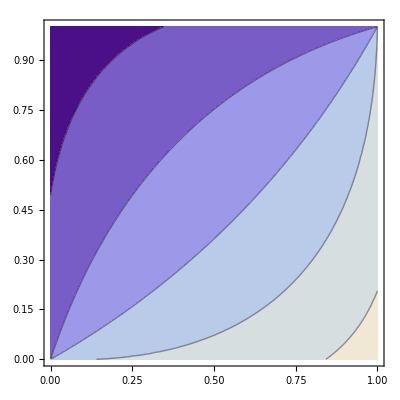

```mathematica
ContourPlot[rho,{x,0,1},{y,0,1}]
```

```mathematica
Clear[x,y]
rho
```

((0.51 (-1+x)+0.49 (-1+y)) (0.4743 x+0.3577 y))/((0.4437 (-1+x)+0.3381 (-1+y)) (0.51 x+0.49 y))

```mathematica
Solve[rho==1, {x,y}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Solve::svars: Equations may not give solutions for all "solve" variables.

{{y→1.25382×10^-29 (-1.05393×10^29-1.03765×10^29 x-1. √(1.11076×10^58+7.1933×10^58 x+4.30686×10^56 x^2))},{y→1.25382×10^-29 (-1.05393×10^29-1.03765×10^29 x+√(1.11076×10^58+7.1933×10^58 x+4.30686×10^56 x^2))}}

```mathematica
4
```